# Stats Practice and Data Analysis II

## 0. Meeting Mathematica’s LinearModelFit

In lab lecture we showed that one can use the method of least squares to find the best estimates of the parameters in a linear model. A line is a type of linear model. When expressed in this form

y = A + B x ,

it is clear that parameter A is the y-intercept and B is the slope; y is the one and only dependent variable and x is the one and only independent variable. For any linear model, the best estimates of the parameters can be found merely from the input data, which also allows uncertainties to be propagated to these parameter estimates. Doing that work, we would arrive at the best values for the y-intercept, slope and x-intercept (naming this ‘C’) to be given by

A_best = 1/Δ[(∑_(i=1)^N y_i)(∑_(i=1)^N x_i^2)-(∑_(i=1)^N x_i)(∑_(i=1)^N x_i y_i)]

B_best = 1/Δ[N(∑_(i=1)^N x_i y_i)-(∑_(i=1)^N x_i)(∑_(i=1)^N y_i)]

C_best = -A_best/B_best

where

Δ=N( ∑_(i=1)^N x_i^2)-(∑_(i=1)^N x_i)^2 .

Note that these assume uniform uncertainties in the dependent variable y. We can actually use the fit to estimate of the uncertainty in the y values as:

σ_y=√(1/(N-2)∑_(i=1)^N (y_i-A - B x_i)^2)

and the uncertainties in the y-intercept, slope and x-intercept are then given by

σ_A=σ_y √(1/Δ∑_(i=1)^N x_i^2)

σ_B=σ_y √(N/Δ)

σ_C=σ_y/B_best^2 √((B_best(∑_(i=1)^N x_i y_i)+A_best(∑_(i=1)^N y_i))/Δ).

Mathematica’s function LinearModelFit will use exactly these formulae to calculate these parameters if you tell it you’d like to just fit a linear model of a single variable, ‘x’ (otherwise known as a line). It automatically assumes you’d like to fit the y-intercept as well. (For much more info on LinearModelFit, see its documentation. You can also fit linear models of more complicated functions, including higher power polynomials.) The function LinearModelFit requires three parameters: 1) the data itself as a list of {x,y} pairs, 2) a list of the functions the linear parameter(s) are to be multiplied by (here just ‘x’) and a list of what the variables are in these specified functions (again, here, just ‘x’).  What follows is a very basic example of how to use LinearModelFit to fit a line.

First, we generate some data:

```mathematica
xvalues=Table[i,{i,1,10}]
yvalues := xvalues+RandomVariate[NormalDistribution[]]
data = Table[{xvalues[[i]],yvalues[[i]]},{i,1,10}]
```

{1,2,3,4,5,6,7,8,9,10}

{{1,0.900923},{2,0.810117},{3,3.44333},{4,3.64494},{5,3.81979},{6,6.07284},{7,6.8091},{8,8.43964},{9,7.89201},{10,9.40693}}

Next, perform the fit.

```mathematica
lm=LinearModelFit[data,{x},{x}]
```

FittedModel[-0.304519+0.986997 x]

This variable “lm” now stores an object representing all the info gained in performing the fit. We can access the parameters and their errors as follows. The first parameter is the y-intercept and the second is the slope (these are just lists, you can extract a value if you like, as shown. There is also an option to print out a ParameterTable with all at once.

```mathematica
lm["BestFitParameters"]
yint=lm["BestFitParameters"][[1]]
lm["ParameterErrors"]
```

{-0.304519,0.986997}

-0.304519

{0.453623,0.073108}

```mathematica
lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.304519 | 0.453623 | -0.671304 | 0.520935
x | 0.986997 | 0.073108 | 13.5005 | 8.69415×10^-7

The estimated error on the y-values can be obtained as:

```mathematica
sigy=Sqrt[lm["EstimatedVariance"]]
```

0.664036

We can plot the data and best-fit line as follows:

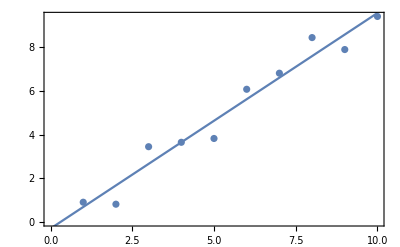

```mathematica
Show[ListPlot[data],Plot[lm[x],{x,0,10}],Frame->True]
```

Usually, you’ll have errors to add to your plots featuring experimental data. Here’s one way to do that.

{{1,0.01.0},{2,2.71.0},{3,2.11.0},{4,3.91.0},{5,5.01.0},{6,6.61.0},{7,6.51.0},{8,9.81.0},{9,8.21.0},{10,10.81.0}}

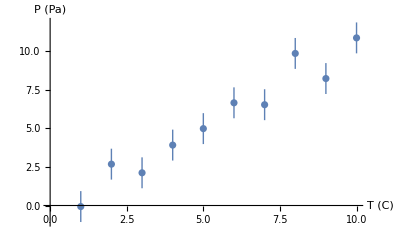

```mathematica
dataWithErrors = Table[{xvalues[[i]],Around[yvalues[[i]],1]},{i,1,Length[xvalues]}]
P1 = ListPlot[dataWithErrors,AxesLabel-> {"T (C)", "P (Pa)"}]
```

## 1. Fitting Millikan’s photoelectric effect data

Often it is convenient to take data in lab in Excel and then import that data into Mathematica for analysis

Download the file StatLab2Data.xlsx from the Moodle

In Excel, create a new notebook and paste in just the frequency and voltage values.  Save this as StatLab2Data.csv in the comma-separated-values (CSV) format

You can import this data into Mathematica using MillikanData = Import[“Desktop/StatLab2Data.csv”] assuming that you saved your file to the desktop.  If you saved it somewhere else, you’ll have to change the path accordingly (Insert > FilePath can be useful here).  Verify that MillikanData contains the data from your Excel spreadsheet.

```mathematica
MillikanData=Import["Documents/StatLab2Data.csv"]
```

{{54.9,-2.05},{69.2,-1.5},{74.2,-1.31},{82.2,-0.93},{96.1,-0.39},{118.3,0.51}}

The data that you have imported contains Millikan’s actual data. Frequencies are in 10^13 Hz, potentials are in volts. The relevant equation is E = e V = h f - ϕ, where e is the charge of the electron, V the voltage, h Planck’s constant, f the frequency and ϕ is related to the ‘work function’ for the specific metal used. The established value for Planck’s constant is h=4.135667 10^-15 eV s. Millikan claimed that each voltage measurement was accurate to 0.02 Volt.

Make a plot of the data with error bars.

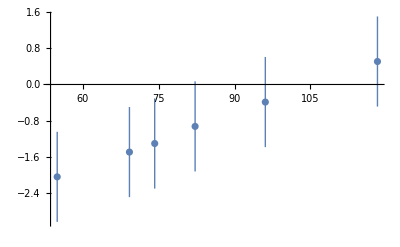

```mathematica
xvalues2={54.9,69.2,74.2,82.2,96.1,118.3};
yvalues2={-2.05,-1.5,-1.31,-0.93,-0.39,0.51};
dataWithErrors2 = Table[{xvalues2[[i]],Around[yvalues2[[i]],1]},{i,1,Length[xvalues2]}];
P2 = ListPlot[dataWithErrors2]
```

Fit the data and create a plot showing both the data and the fit. Note that you can combine multiple plots with the Show command.

FittedModel[-4.29675+0.0406355 x]

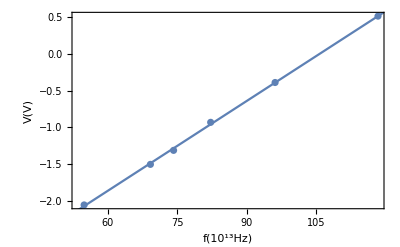

```mathematica
data2 = Table[{xvalues2[[i]],yvalues2[[i]]},{i,1,6}];
lm2=LinearModelFit[MillikanData,{x},{x}]
Show[ListPlot[MillikanData],Plot[lm2[x],{x,0,120}],Frame->True,AxesLabel-> {"f(10^13Hz)", "V(V)"}]
```

Find Millikan’s experimental value for Planck’s constant and its error.

Calculate the residuals (the differences between y_i and A + B x_i for each point) and plot them as a function of frequency. Plots like these can be helpful to diagnose model inadequacies (i.e. if any trend is seen in the residuals) and tell us whether the initial estimated experimental errors are reasonable or not. Does there seem to be any such trend here?

Compare the σ_y obtained from your fit to Millikan’s claimed experimental error of 0.02 Volts. Comment about what this tells you.

```mathematica
lm2["BestFitParameters"];
yint=lm2["BestFitParameters"][[1]];
lm2["ParameterErrors"];
sigy=Sqrt[lm2["EstimatedVariance"]]
```

0.0223389

## 2. Writing your own ErrorOnXIntercept function

As we mentioned in class, we can easily find the x-intercept from the y-intercept and slope, however, the errors are correlated on those quantities and so we may not use standard error propagation to compute the error on the x-intercept. However, we can propagate uncertainties all the way from the original data values (assumed to be in y only) through to the estimate of the error on the x-intercept as per these formulae

σ_C=σ_y/B_best^2 √((B_best(∑_(i=1)^N x_i y_i)+A_best(∑_(i=1)^N y_i))/Δ)

with

Δ=N( ∑_(i=1)^N x_i^2)-(∑_(i=1)^N x_i)^2 .

First, here is an example using a Module with the internal (or “throwaway-when-done”) variables: sumxsq, sumx, N. Note how it uses the Sum function to perform the sums needed to compute Δ.

```mathematica
Delta[xval_]:= Module[{sumxsq,sumx,N},
N=Length[xval];
sumxsq=Sum[xval[[i]]^2,{i,N}];
sumx=Sum[xval[[i]],{i,N}];
N sumxsq-sumx^2]
```

Below is a start to defining a Module to create the function ErrorOnXIntercept. Some recommended internal variables are provided as well as starting you out with a value for delta and sigy. Use the formula above to complete the function. You will need this below and in some of the experimental labs, so it’s worth putting the time in to make it correct now!

```mathematica
ErrorOnXIntercept[xval_,yval_]:=Module[{N,lm,sigy,Bbest,Abest,delta,sumxy,sumy},
lm=LinearModelFit[Table[{xval[[i]],yval[[i]]},{i,Length[xval]}],x,x];
sigy=Sqrt[lm["EstimatedVariance"]];
delta=Delta[xval];
N=Length[xval];
Abest=lm["BestFitParameters"][[1]];
Bbest=lm["BestFitParameters"][[2]];
sumxy=Sum[xval[[i]]*yval[[i]],{i,N}];
sumy=Sum[yval[[i]],{i,N}];
xint=-Abest/Bbest;
sigc=(sigy/Bbest^2)*Sqrt[((Bbest*Sum[xval[[i]]*yval[[i]],{i,N}])+(Abest*Sum[yval[[i]],{i,N}]))/delta];
{xint,sigc}
]
```

## 3. Fitting experimental data to find absolute zero

Here we have pressure data for Helium obtained at temperatures between 10 and 100 degrees C. Because we aren’t working in Kelvin for which the PV=nRT form of the ideal gas law holds, we’ll have a linear relationship, but not a proportional one. We will use the data to solve for the zero temperature of the Kelvin scale. We estimate we can read our pressure gauge accurately to 200 Pa.

Temperature in degrees C and pressure in Pa:

```mathematica
T=Table[i*10,{i,1,10}];
P={23400,24400,25000,25200,26400,28000,28400,29200,30200,30800};
err = 200;
errors = Table[err,{i,1,10}];
```

Use LinearModelFit to fit the data.

```mathematica
lm3=LinearModelFit[Transpose[{T,P}],x,x]
```

FittedModel[22453.3+84.4848 x]

Make a plot that shows both your data (with error bars) and the best-fit line.

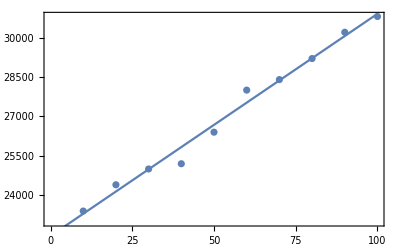

```mathematica
data3=Transpose[{T,P}];
dataWithErrors3= Table[{T[[i]],Around[P[[i]],1]},{i,1,Length[T]}];
Show[ListPlot[dataWithErrors3],Plot[lm3[x],{x,0,100}],Frame->True]
```

Based on your plot and your calculated value of σ_y, do you think the experimenters were correct in how accurately they could read their pressure gauge?

```mathematica
lm3["BestFitParameters"];
yint=lm3["BestFitParameters"][[1]];
lm3["ParameterErrors"];
sigy=Sqrt[lm3["EstimatedVariance"]]
```

318.995

No because their value for sigy is very big.

The x-intercept of your graph should be absolute zero.  Obtain its value and its uncertainty.  Is your result consistent with the accepted value?

```mathematica
xint=-Abest/Bbest
```

-Abest/Bbest

How many σ away from the expected answer is your result?  To calculate this you take the discrepancy (the magnitude of the difference between the experimental and accepted value) and divide by the uncertainty in your experimental value.

## 4. Classic issues in fitting a line

In 1973, statistician F. J. Anscombe published a paper, “Graphs in Statistical Analysis” which succinctly presents some major pitfalls of performing fits to data without paying more attention to what is going on. In particular, 4 data sets were presented whose linear fits are nearly identical and whose sample standard deviations in y are also nearly identical. However, inspection clearly shows that one is a good fit of the data and the other three are poor, or at least not yet well motivated fits.

Data:

3.00009+0.500091 x

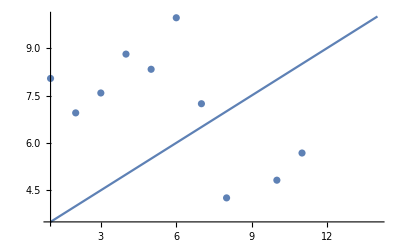

3.00091+0.5 x

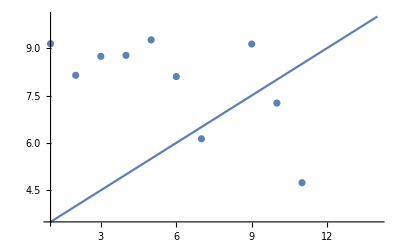

3.00245+0.499727 x

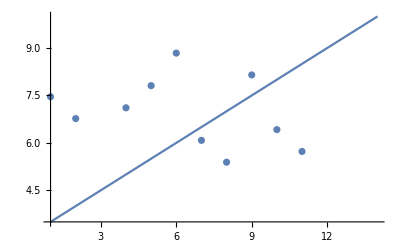

3.00173+0.499909 x

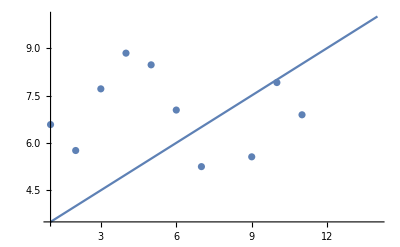

```mathematica
x1={10,8,13,9,11,14,6,4,12,7,5};
y1={8.04,6.95,7.58,8.81,8.33,9.96,7.24,4.26,10.84,4.82,5.68};
Fit[Transpose[{x1,y1}],{1,x},x]
Show[{Plot[%,{x,1,14}],ListPlot[{y1}]}]

x2={10,8,13,9,11,14,6,4,12,7,5};
y2={9.14,8.14,8.74,8.77,9.26,8.1,6.13,3.1,9.13,7.26,4.74};
Fit[Transpose[{x2,y2}],{1,x},x]
Show[{Plot[%,{x,1,14}],ListPlot[{y2}]}]

x3={10,8,13,9,11,14,6,4,12,7,5};
y3={7.46,6.77,12.74,7.11,7.81,8.84,6.08,5.39,8.15,6.42,5.73};
Fit[Transpose[{x3,y3}],{1,x},x]
Show[{Plot[%,{x,1,14}],ListPlot[{y3}]}]

x4={8,8,8,8,8,8,8,19,8,8,8};
y4={6.58,5.76,7.71,8.84,8.47,7.04,5.25,12.5,5.56,7.91,6.89};
Fit[Transpose[{x4,y4}],{1,x},x]
Show[{Plot[%,{x,1,14}],ListPlot[{y4}]}]
```

For each data set, fit the data to a straight line and plot the data along with the fit.

How do the fit parameters, their uncertainties, and the estimate of σ_y compare for the different fits?

Extra Credit: We, as humans, can more or less see what is going wrong with fitting to each of these distributions. Consider potential quantitative ways to distinguish between these fits. Try out some ideas and show at least one computed quantity [other than the nth element] that distinguishes these four datasets.